```mathematica
(* Mathematica*)
<<ComputationalGeometry`
```

```mathematica
Clear[r,phi,pa,pts]
```

```mathematica
pa[x_]=(-1.1754857800810619+x) ((0.-0.8507121199977765 ⅈ)+x) ((0.+0.8507121199977765 ⅈ)+x) (1.1754857800810619+x)
```

(-1.17549+x) ((0.-0.850712 ⅈ)+x) ((0.+0.850712 ⅈ)+x) (1.17549+x)

```mathematica
a0={Re[x],Im[x]}/.NSolve[pa[x]==0,x]
```

{{-1.17549,0},{0.,-0.850712},{0.,0.850712},{1.17549,0}}

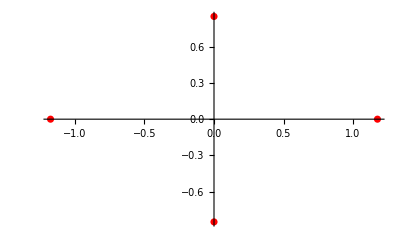

```mathematica
ListPlot[a0,PlotStyle->Red,PlotRange->All]
```

```mathematica
Length[a0]
```

4

```mathematica
pts=Union[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pa[x]==0,x]]//Chop
```

{{-0.98707,0,-0.160287},{0,-0.98707,0.160287},{0,0.98707,0.160287},{0.98707,0,-0.160287}}

```mathematica
ptsn=Table[Hue[Norm[x/.NSolve[pa[x]==0,x][[i]]]/1.75],{i,Length[pts]}]
```

{Hue[0.671706160046321],Hue[0.48612121142730086],Hue[0.48612121142730086],Hue[0.671706160046321]}

```mathematica
(* Voronoi diagram*)
```

```mathematica
a=Union[Most/@pts];
```

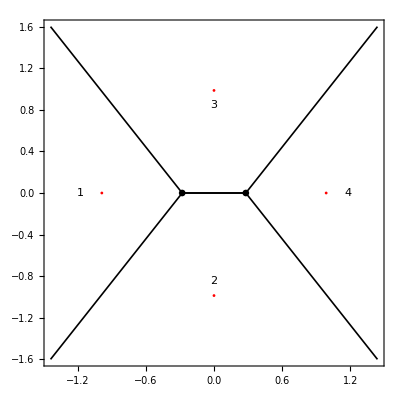

```mathematica
g1=Show[{
DiagramPlot[a0],
Graphics[{Red,PointSize[.005],Point[a]}]
},PlotRange->All,Frame->True,ImageSize->Full]
```

```mathematica
g2=Show[Graphics3D[{Red,PointSize[0.0375/3],Point/@pts}],Axes->True,ImageSize->1000,ViewPoint->{5,5,5}]
```

-Graphics3D-

```mathematica
(*(* Voronoi diagram*)
g1=Show[{
DiagramPlot[a0,LabelPoints->False]/._Point:>{},
Graphics[{Red,PointSize[.005],Point[a0]}]
},PlotRange->All,Frame->True,PlotRangeClipping->True,ImageSize->1000]
(* 3d projection of polyhedron*)*)
```

```mathematica
(* convex hull: MathWorld Library*)
<<ConvexHull`
```

```mathematica
hull0=ConvexHull3D[pts]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
ga=Show[Graphics3D[ConvexHull3D[pts]]]
```

-Graphics3D-

```mathematica
Length[hull0]
```

4

```mathematica
gb=hull1=Show[Graphics3D[Flatten[Table[If[i≤Length[ptsn],{ptsn[[i]],hull0[[i]]},{}],{i,Length[hull0]}]]]]
```

-Graphics3D-

```mathematica
hull3=Show[{ga,gb},ViewPoint->{3,3,3}]
```

-Graphics3D-

```mathematica
(*Export["x36_Riley_example_2nd_Polynomial_convex_Hull.jpg",{g1,g2,hull3}]*)
(*end*)
```